## Лабораторная работа №1

# Задание 1

```mathematica
Uzl={0.1, 0.2,0.3,0.4};
```

```mathematica
Znach={-1.02,2.640,-5.850,8.540};
```

```mathematica
n=Length[Uzl]-1;
```

```mathematica
Do[{Subscript[x, i]=Uzl[[i+1]],Subscript[y, i]=Znach[[i+1]]},{i,0,n}]
```

```mathematica
e=1/2*10^-3;
```

```mathematica
m1=1;
```

```mathematica
m2=2;
```

```mathematica
Do[Subscript[t, i]=∑_(k=0)^n Subscript[x, k]^i,{i,0,2m1}];
```

```mathematica
Do[ Subscript[c, i]=∑_(k=0)^n Subscript[y, k] Subscript[x, k]^i,{ i,0,m1}];
```

```mathematica
eqv=Table[∑_(i=0)^m1 Subscript[a, i] Subscript[t, i+k]==Subscript[c, k],{k,0,m1}]
```

{4. a_0+1. a_1==4.31,1. a_0+0.3 a_1==2.087}

```mathematica
Koef=Solve[eqv,{}]//Flatten;
```

```mathematica
P[x_]=(∑_(i=0)^m1 Subscript[a, i]*x^i)/.Koef
```

-3.97+20.19 x

```mathematica
Tbl=Table[{Subscript[x, k],Subscript[y, k]},{k,0,n}];
```

```mathematica
Fun=Table[x^i,{i,0,m1}];
```

```mathematica
P1[x_]=Fit[Tbl,Fun,x]
```

-3.97+20.19 x

```mathematica
P[x]==P1[x]
```

True

```mathematica
γ=√(1/(n+1)*∑_(k=0)^n (P[Subscript[x, k]]-Subscript[y, k])^2)//N
```

4.74706

```mathematica
γ>e
```

True

```mathematica
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
```

```mathematica
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
```

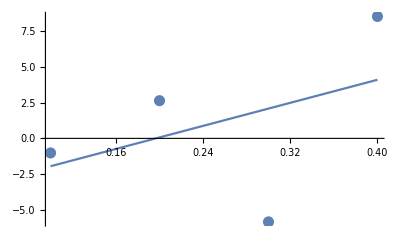

```mathematica
Show[Gr1,Gr2]
```

```mathematica
Do[Subscript[t, i]=∑_(k=0)^n Subscript[x, k]^i,{i,0,2m2}];
```

```mathematica
Do[ Subscript[c, i]=∑_(k=0)^n Subscript[y, k] Subscript[x, k]^i,{ i,0,m2}];
```

```mathematica
eqv=Table[∑_(i=0)^m2 Subscript[a, i] Subscript[t, i+k]==Subscript[c, k],{k,0,m2}]
```

{4. a_0+1. a_1+0.3 a_2==4.31,1. a_0+0.3 a_1+0.1 a_2==2.087,0.3 a_0+0.1 a_1+0.0354 a_2==0.9353}

```mathematica
Koef=Solve[eqv,{}]//Flatten;
```

```mathematica
P[x_]=(∑_(i=0)^m2 Subscript[a, i]*x^i)/.Koef
```

9.4425-113.935 x+268.25 x^2

```mathematica
Tbl=Table[{Subscript[x, k],Subscript[y, k]},{k,0,n}];
```

```mathematica
Fun=Table[x^i,{i,0,m2}];
```

```mathematica
P1[x_]=Fit[Tbl,Fun,x]
```

-10.1217+123.313 x-289.225 x^2

```mathematica
P[x]==P1[x]
```

9.4425-113.935 x+268.25 x^2==-3.97+20.19 x

```mathematica
γ=√(1/(n+1)*∑_(k=0)^n (P[Subscript[x, k]]-Subscript[y, k])^2)//N
```

3.91647

```mathematica
γ>e
```

True

```mathematica
k1=γ/e
```

7832.95

```mathematica
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
```

```mathematica
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
```

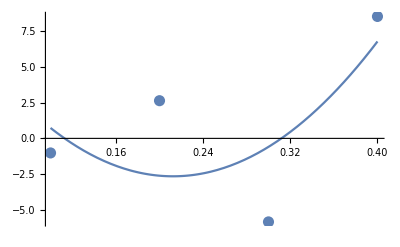

```mathematica
Show[Gr1,Gr2]
```

# Задание 2

```mathematica
m3=3;
```

```mathematica
Do[Subscript[t, i]=∑_(k=0)^n Subscript[x, k]^i,{i,0,2m3}];
```

```mathematica
Do[ Subscript[c, i]=∑_(k=0)^n Subscript[y, k] Subscript[x, k]^i,{ i,0,m3}];
```

```mathematica
eqv=Table[∑_(i=0)^m3 Subscript[a, i] Subscript[t, i+k]==Subscript[c, k],{k,0,m3}]
```

{4. a_0+1. a_1+0.3 a_2+0.1 a_3==4.31,1. a_0+0.3 a_1+0.1 a_2+0.0354 a_3==2.087,0.3 a_0+0.1 a_1+0.0354 a_2+0.013 a_3==0.9353,0.1 a_0+0.0354 a_1+0.013 a_2+0.00489 a_3==0.40871}

```mathematica
Koef=Solve[eqv,{}]//Flatten;
```

```mathematica
P[x_]=(∑_(i=0)^m3 Subscript[a, i]*x^i)/.Koef
```

-51.86+861.067 x-4110.5 x^2+5838.33 x^3

```mathematica
Tbl=Table[{Subscript[x, k],Subscript[y, k]},{k,0,n}];
```

```mathematica
Fun=Table[x^i,{i,0,m3}];
```

```mathematica
P1[x_]=Fit[Tbl,Fun,x]
```

9.4425-113.935 x+268.25 x^2

```mathematica
(P[x]-P1[x])//Chop
```

-61.3025+975.002 x-4378.75 x^2+5838.33 x^3

```mathematica
γ=√(1/(n+1)*∑_(k=0)^n (P[Subscript[x, k]]-Subscript[y, k])^2)//N
```

8.47868×10^-12

```mathematica
k2=e/γ
```

5.89714×10^7

```mathematica
If[k1<k2,opt=2,3]
```

2

```mathematica
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
```

```mathematica
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
```

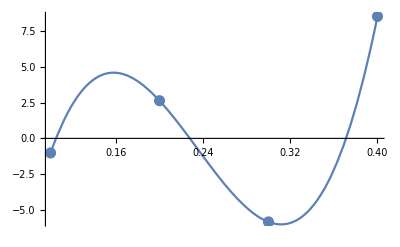

```mathematica
Show[Gr1,Gr2]
```